```mathematica
md=getMapData[mapList[[6]]][All,{"KL","piTtt","MFP","etaTtt"}];
```

```mathematica
mdg=md[GroupBy["KL"]];
```

```mathematica
front=Table[mdg[[i]][{1,-2},{"piTtt","MFP"}]//Normal//Values,{i,1,3}]
```

{{{1.23531,0.549848},{1.29459,0.609607}},{{1.42076,0.671393},{1.52237,0.730834}},{{1.63051,0.757439},{1.80228,0.815381}}}

```mathematica
end=Table[mdg[[i]][-1,{"piTtt","MFP"}]//Normal//Values,{i,4,Length[mdg]}]
```

{{2.11621,0.857119},{2.42625,0.87891},{2.79462,0.889387},{3.25505,0.894931},{3.65287,0.896795}}

```mathematica
line=Partition[Flatten[Append[front,end]],2]
```

{{1.23531,0.549848},{1.29459,0.609607},{1.42076,0.671393},{1.52237,0.730834},{1.63051,0.757439},{1.80228,0.815381},{2.11621,0.857119},{2.42625,0.87891},{2.79462,0.889387},{3.25505,0.894931},{3.65287,0.896795}}

```mathematica
int=Interpolation[line,Method->"Spline",InterpolationOrder->1]
```

InterpolatingFunction[…]

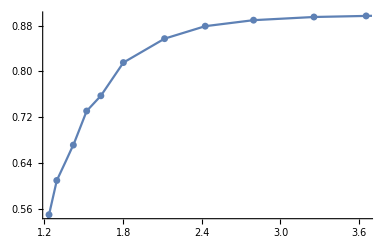

```mathematica
Show[ListPlot[line],Plot[int[x],{x,1,4}]]
```